```mathematica
TriangleCenterOfMass[imageFilename_,mask_]:=Block[{},
picture=Import[imageFilename];
maskedPicture=ImageSubtract[picture,ColorNegate[mask]];
binarizedPicture=Binarize[maskedPicture,0.98];
components=MorphologicalComponents[binarizedPicture];
componentIndices=MapIndexed[If[#1>0.5,{#2⟦2⟧,#2⟦1⟧},{0,0}]&,components,{2}];
N[Mean[Select[Flatten[componentIndices,{2,1}],#≠{0,0}&]]]
]
```

```mathematica
mask=Import["/Users/hortont/Documents/School/RPI/2010 (Senior)/Computational Vision/final project/focus/1/mask.jpg"];
filenames=Map["/Users/hortont/Documents/School/RPI/2010 (Senior)/Computational Vision/final project/focus/1/"<>ToString[#]<>".jpg"&,Range[11]];
outfilenames=Map["/Users/hortont/Documents/School/RPI/2010 (Senior)/Computational Vision/final project/focus/1/scaled-"<>ToString[#]<>".jpg"&,Range[11]];
```

```mathematica
coms=Map[TriangleCenterOfMass[#,mask]&,filenames];
```

```mathematica
comPairs=Thread[{{1,1.189,1.251,1.496,1.778,1.995,2.511,2.985,4.217,6.310,21.135},coms}];
```

```mathematica
comPairs//MatrixForm
```

(1 | {3494.78,2380.06}
1.189 | {3488.29,2374.68}
1.251 | {3484.12,2368.08}
1.496 | {3480.53,2358.41}
1.778 | {3481.29,2334.41}
1.995 | {3472.86,2335.19}
2.511 | {3455.65,2343.83}
2.985 | {3442.81,2347.6}
4.217 | {3432.7,2346.2}
6.31 | {3424.17,2341.86}
21.135 | {3416.02,2337.47})

```mathematica
distPairs=Map[{#⟦1⟧,Norm[#⟦2⟧-{3872/2,2592/2}]}&,comPairs];
primaryDistPair=Last[distPairs]; (* this needs to take max, which might not always be the last one *)
otherDistPairs=Most[distPairs];
```

```mathematica
scales=Map[{#⟦1⟧,#⟦2⟧/primaryDistPair⟦2⟧}&,otherDistPairs];
dataPlot=ListPlot[scales,PlotStyle->PointSize[0.015]];
```

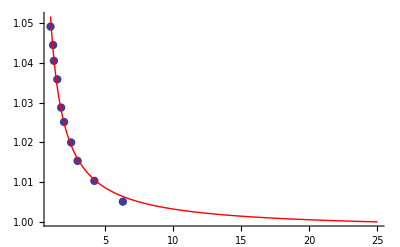

```mathematica
model=a*x^-1+b;
fit=FindFit[scales,model,{a,b},x];

Show[{dataPlot,Plot[Evaluate[model/.fit],{x,1,25},PlotStyle->{Thick,Red},PlotRange->Full]}]
```

```mathematica
fit
```

{a→0.0538741,b→0.99783}

```mathematica
model/.fit/.x->1
```

1.0517